```mathematica
dataPath=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"data/dataOccupancyPreprocessed.csv"}];
```

```mathematica
data=SemanticImport[dataPath,{"DateTime","Real","Real","Real","Real","Real","Boolean"},"Dataset",HeaderLines->1];
```

```mathematica
trainData=Values@Normal[data[[All,{"Temperature","Humidity","Light","CO2","HumidityRatio"}]]];
```

```mathematica
cluster[method_:"GaussianMixture",numberClusters_:2,distanceFunction_:EuclideanDistance]:=Module[{clusters,rules,classifier},
clusters=ClusteringComponents[trainData,numberClusters,1,Method->method,DistanceFunction->distanceFunction,PerformanceGoal->"Quality"];
rules=Map[clusters[[#]]->data[[#,"Occupancy"]]&,Range[Length[data]]];
classifier=Classify[rules,Method->Automatic];
Return[ClassifierMeasurements[classifier,rules]];
]
```

```mathematica
cm=cluster["KMeans",2,ManhattanDistance];
```

```mathematica
cm["ClassMeanCrossEntropy"]
```

<|False→0.108652,True→0.464256|>

```mathematica
cm["Accuracy"]
```

0.941604

```mathematica
cm["FScore"]
```

<|False→0.962747,True→0.864958|>

```mathematica
cm["ClassMeanCrossEntropy"]
```

<|False→0.108652,True→0.464256|>

```mathematica
cm["Specificity"]
```

<|False→0.937018,True→0.942747|>

```mathematica
cm["Perplexity"]
```

1.19677

```mathematica
cm["Precision"]
```

<|False→0.983614,True→0.803189|>

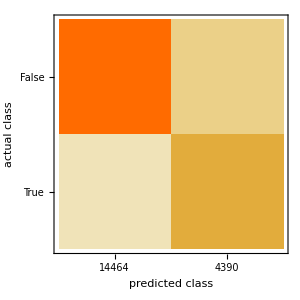

```mathematica
cm["ConfusionMatrixPlot"]
```

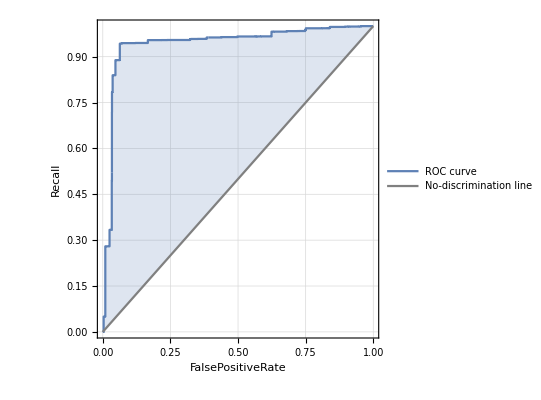
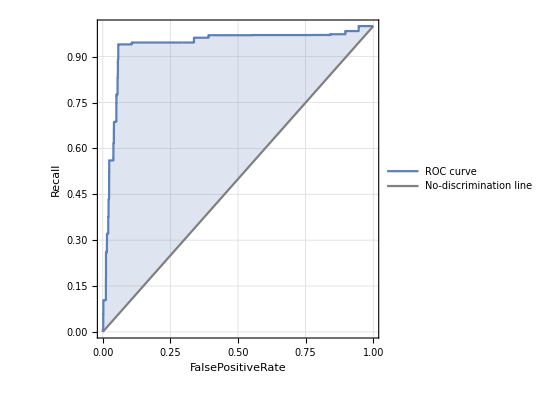
<|False→-Graphics-,True→-Graphics-|>

```mathematica
cm["ROCCurve"]
```